```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Import data

```mathematica
geo=Import["Municipios_Colombia.geojson",{"GeoJSON","Data"}];
(* how does mathematica manages to import a geoJSON so poorly? *)
geometries=AssociationThread[geo[[2,2,All,1,2]]->geo[[2,2,All,-1,2]]];
```

#### Functions

```mathematica
GeoElevationFromPolygon[polygon_,resolution_:Quantity[1,"Kilometers"]]:=QuantityMagnitude@GeoElevationData[
polygon,
GeoResolution->resolution
]
```

#### Example

```mathematica
GeoGraphics[{
GeoStyling["ReliefMap",Directive[EdgeForm[Black],Opacity[0.6]]],
geometries["05001"]
}]
```

-Graphics-

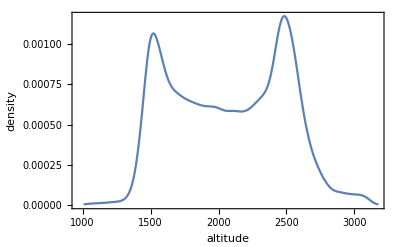

```mathematica
SmoothHistogram[
Flatten@GeoElevationFromPolygon[geometries["05001"],Quantity[50,"Meters"]],
Frame->True,FrameLabel->{"altitude","density"}
]
```

### Query all municipalities

```mathematica
elevations=Flatten/@GeoElevationFromPolygon/@geometries;
elevations=Select[#>0&]/@elevations;
```

```mathematica
means=Mean/@elevations;
```

```mathematica
Export["altitud.csv",Dataset@means,"CSV",TableHeadings->{"id","altitud"}]
```

altitud.csv